```mathematica
Needs["QuantumWalks`"]
```

```mathematica
?QuantumWalks`*
```

```mathematica
?ExpValPosition
```

## Packages and nb definitions

```mathematica
c[ρ_,α_]:={{Exp[I*α]Sqrt[ρ],I*Sqrt[1-ρ]},{I*Sqrt[1-ρ],Exp[-I*α]Sqrt[ρ]}}
```

```mathematica
ClearAll[DTQWFlitney2012]
DTQWFlitney2012[ψ0_,coinCombination_,reps_]:=Fold[Chop@ArrayPad[DTQWStep[#2[[1]],#2[[2]]].#1,2]&,ArrayPad[ψ0,2],Transpose[{Range[Length[coinCombination]*reps],Catenate[ConstantArray[coinCombination,reps]]}]]
```

## AB

```mathematica
ρ=1/2.;
α=0.005;
β=0.005;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=50;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-0.148213

```mathematica
expvalx=Table[
ψ=DTQWFlitney2012[ψ0,coinCombination,reps];
{reps,Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]}
,{reps,0,100}];
```

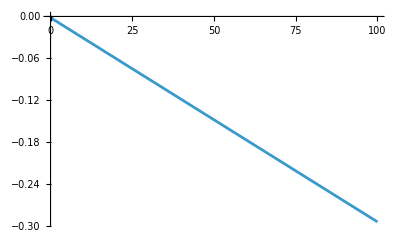

```mathematica
ListPlot[expvalx,
Joined->True]
```

## ABB

```mathematica
ρ=1/2.;
α=0.;
β=Pi/2.;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=33;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-9.656

## ABBB

```mathematica
ρ=1/2.;
α=0.01;
β=1.2;

A=c[ρ,α];
B=c[ρ,β];

coinCombination={A,B,B,B};
```

```mathematica
ψ0=N@Normalize[{1,-1}];
reps=25;

ψ=DTQWFlitney2012[ψ0,coinCombination,reps];

Chop[ExpValPosition[ψ,Length[coinCombination]*reps]]
```

-16.6787